# Jacobi Elliptic Functions

## According to the definition, m=k^2

```mathematica
ClearAll["Global`*"]
```

```mathematica
sn[q_,k_]:=JacobiSN[q,k];
cn[q_,k_]:=JacobiCN[q,k];
dn[q_,k_]:=JacobiDN[q,k];
```

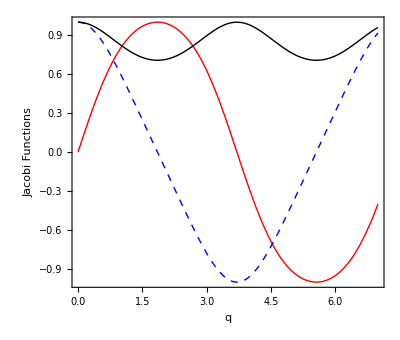

```mathematica
Plot[{sn[q,1/2],cn[q,1/2],dn[q,1/2]},{q,0,7},Frame->True,Axes->{True,False},AspectRatio->0.85,FrameStyle->Directive[Black,Thick],FrameLabel->{"q","Jacobi Functions"},LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},PlotStyle->{{Red,Thick},{Blue,Thick,Dashed},{Black,Thick}}]
```